## Quantum Phase Estimation Algorithm

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Eigenvalue

Eigenvector

### Eigenvectors and Eigenvalues

Eigenvectors and eigenvalues are concepts from the theory of linear algebra, and they are frequently used in analyzing the solutions of all sorts of mathematical models.

From linear algebra and the theory of matrices, you should recall that an n×n matrix acting on an n dimensional vector will give another n dimensional vector. In the case of real numbers, it is only the case that a x=b x if a=b or x=0. For square matrices, it is possible to have A x⃗=λ x⃗ for a real number, λ. When this happens x⃗ is called an eigenvector of A and λ is the corresponding eigenvalue of A.

As an example, consider the matrix corresponding to the Pauli Z operator in the computational basis:

```mathematica
QuantumOperator["Z"]["Matrix"]//MatrixForm//TraditionalForm
```

(1 | 0
0 | -1)

You can compute the eigenvalues and eigenvectors of this matrix using the Eigensystem function:

```mathematica
Eigensystem[QuantumOperator["Z"]["Matrix"]]
```

{{-1,1},{{0,1},{1,0}}}

These are the lists of eigenvalues followed by the eigenvectors. Let’s look at them in the form λ_i->(x⃗)_i:

```mathematica
QuantumOperator["Z"]["Eigensystem"]//MapThread[Rule]
```

{-1→{0,1},1→{1,0}}

You can see from the eigenvectors that the state 0 corresponds to the positive eigenvalue of the Pauli Z operator. Similarly, the state 1 corresponds to the negative eigenvalue of the Pauli Z operator.

```mathematica
QuantumBasis["Computational"]["ElementAssociation"]
```

<|0→{1,0},1→{0,1}|>

```mathematica
QuantumBasis["Z"]["ElementAssociation"]
```

<|𝓏_+→{1,0},𝓏_−→{0,1}|>

#### Example

Compute eigenvalues and eigenvectors of the matrix (3 | 4
1 | 3).

##### Solution

Automate the computation:

```mathematica
Eigensystem[{{3,4},{1,3}}]
```

{{5,1},{{2,1},{-2,1}}}

The eigenvector (2
1) has eigenvalue 5 and the eigenvector (-2
1) has eigenvalue 1.

Check that this is indeed the case:

```mathematica
(A.x==λ x)/.{A->{{3,4},{1,3}},x->{2,1},λ->5}
```

True

```mathematica
(A.x==λ x)/.{A->{{3,4},{1,3}},x->{-2,1},λ->1}
```

True

### Quantum Phase Estimation

Gate operators in a quantum circuit can be represented as unitary matrices. Recall from the lesson on quantum operators that a unitary matrix is defined by the property that U†=U^-1. In Wolfram Language, this is equivalent to ConjugateTranspose[U]==Inverse[U].

For a unitary matrix, its eigenvalues are of the form Uλ=ⅇ^(2π ⅈ θ)λ for a real number θ.

Let’s consider such a matrix:

```mathematica
SeedRandom[1234];
Urandom=QuantumOperator["RandomUnitary"]
```

QuantumOperator[…]

Obtain the eigenvalues:

```mathematica
λs=Urandom["Eigenvalues"]
```

{0.429566+0.903035 ⅈ,-0.645446-0.763806 ⅈ}

Find each θ such that λ=ⅇ^(2π ⅈ θ):

```mathematica
θs=Mod[Arg[λs]/(2Pi),1]
```

{0.179333,0.638336}

Check the relation:

```mathematica
λs==Exp[2 Pi I θs]
```

True

These were found using classical means. The quantum phase estimation (QPE) algorithm uses the phenomenon of phase kickback to obtain the values for θ needed to compute the eigenvalues.

Obtain the circuit for this unitary operator:

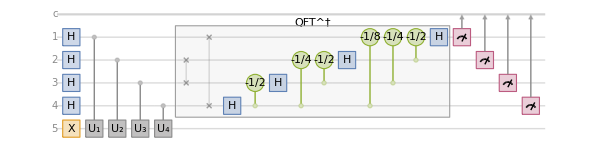

```mathematica
qc1=QuantumCircuitOperator["PhaseEstimation"[Urandom]];
qc1["Diagram",ImageSize->600]
```

Notice a few things about the circuit. First, the first four qubits are put into a superposition, then used as control qubits, then acted on by the inverse quantum Fourier transform, finally measured. Lastly, the fifth qubit is put into the state 1 and then acted on by a sequence of four unitary operators. Each of these unitarity matrices is simply a power of the unitary matrix you began with.

Through this procedure, the base 2 digits of θ will be encoded in the register qubits. Observe what happens when the circuit is run:

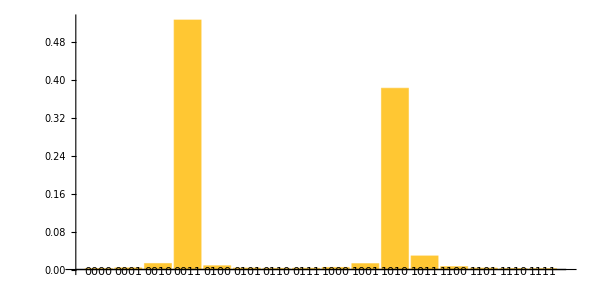

```mathematica
measurements1=N[qc1][];
measurements1["ProbabilityPlot",AspectRatio->1/2,ImageSize->600]
```

The measurement probabilities are strongly peaked around two particular results. These results represent estimates of the values of θ:

```mathematica
results1=KeySort@TakeLargest[measurements1["Probabilities"],2]
```

<|0011→0.526029,1010→0.382148|>

These results can be read as the binary representation of a number between 0 and 1-2^-n, where n was the number of register qubits. In this case, there were four register qubits.

```mathematica
estimates1=Map[FromDigits[#,2]/(2^Length[#])&,First/@Keys@results1]
```

{3/16,5/8}

Compare these estimates to the actual values for θ:

```mathematica
θs==Around[estimates1,2^-4]
```

True

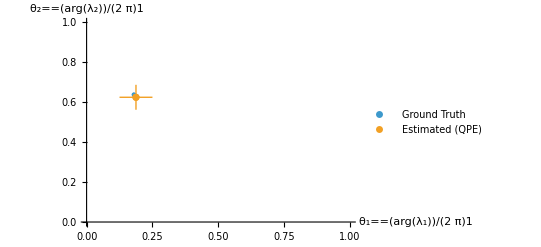

```mathematica
ListPlot[{{θs},{Around[estimates1,2^-4]}},]
```

Within the resolution given by δ=2^-n, the algorithm finds states 2^n x such that x-δ≤θ≤x+δ. Critically, this was done without ever inverting the matrix U. Instead of the classical computational costs of inverting the matrix, you must apply O(n^2) powers of the matrix U in order to obtain resolution δ=2^-n. This comes from the fact that ∑_(k=1)^n k=n(n+1)/2.

### Phase Estimation with Larger Matrices

Consider a larger 4×4 matrix which acts on 2 qubits:

```mathematica
SeedRandom[1234];
Urandom2=QuantumOperator["RandomUnitary"[2,2]]
```

QuantumOperator[…]

This time, there are four eigenvalues:

```mathematica
λ2=Urandom2["Eigenvalues"]
```

{-0.710774-0.70342 ⅈ,0.503335-0.864091 ⅈ,-0.990375-0.138413 ⅈ,0.82902+0.559219 ⅈ}

Find each θ such that λ=ⅇ^(2π ⅈ θ):

```mathematica
θ2=Mod[Arg[λ2]/(2Pi),1]
```

{0.624172,0.833947,0.5221,0.0944495}

Check the relation:

```mathematica
λ2==Exp[2 Pi I θ2]
```

True

Obtain the circuit for this larger unitary operator:

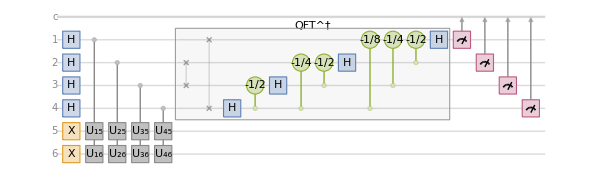

```mathematica
qc2=QuantumCircuitOperator["PhaseEstimation"[Urandom2]];
qc2["Diagram",ImageSize->600]
```

This time, two ancilla qubits are needed so that the 4×4 unitary can act properly on the circuit. Other than this difference, the circuit works following the same principles as before. Controlled operators (corresponding to powers of the matrix under consideration) are used to encode information about the operator’s eigenvalues into the phases of the register qubits. This information is then decoded by measuring the register qubits.

For a 4×4 matrix, four eigenvalues are expected:

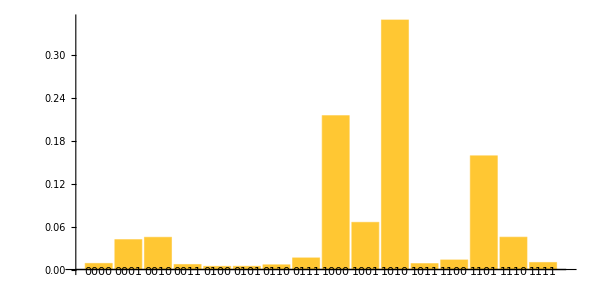

```mathematica
measurements2=N[qc2][];
measurements2["ProbabilityPlot",AspectRatio->1/2,ImageSize->600]
```

Unlike the previous case, it is not so obvious which of these measurement results are supposed to correspond to the four eigenvalues. Let’s proceed with the four most likely outcomes and hope for the best:

```mathematica
results2=KeySort@TakeLargest[measurements2["Probabilities"],4]
```

<|1000→0.215278,1001→0.0659568,1010→0.349102,1101→0.159077|>

Compute the estimates based on the four most likely outcomes:

```mathematica
estimates2=Map[FromDigits[#,2]/(2^Length[#])&,First/@Keys@results2]
```

{1/2,9/16,5/8,13/16}

This time, the actual values for θ were not all captured by the four most likely outcomes:

```mathematica
Sort[θ2]==Around[estimates2,2^-4]
```

False

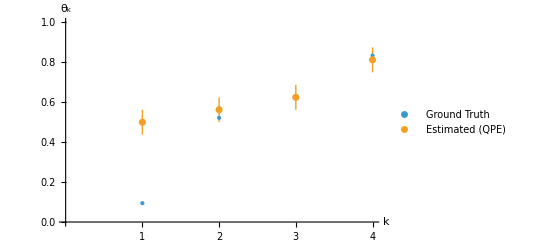

```mathematica
ListPlot[{Sort@θ2,Around[estimates2,2^-4]},]
```

As you can see, one of the values was missed by this circuit. For larger unitary matrices, it is necessary to modify the input state on the ancillary qubits, as the information about the smallest eigenvalue was apparently not captured very successfully by the last circuit.

Define a circuit which is identical except for the state prepared on the ancillary qubits:

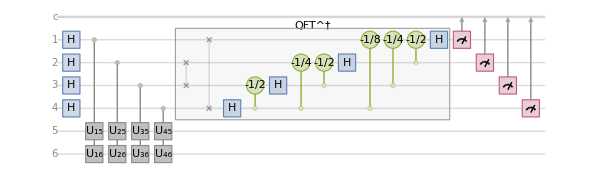

```mathematica
qc3=QuantumCircuitOperator["PhaseEstimation"[Urandom2]][[3;;]];
qc3["Diagram",ImageSize->600]
```

This time, information about the largest eigenvalue is not captured particularly well; however, you do get a clearer signal related to the smallest eigenvalue:

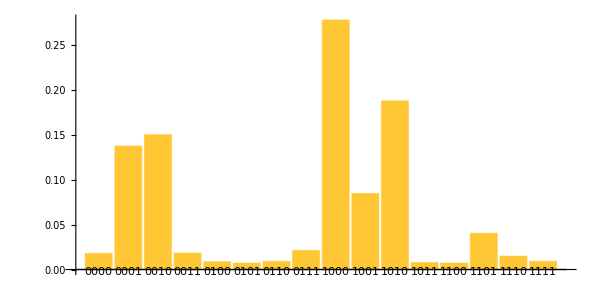

```mathematica
measurements3=N[qc3][];
measurements3["ProbabilityPlot",AspectRatio->1/2,ImageSize->600]
```

Considering the four most likely outcomes from this second circuit, the largest eigenvalue is missed, and the smallest is double-counted:

```mathematica
results3=KeySort@TakeLargest[measurements3["Probabilities"],4]
```

<|0001→0.137514,0010→0.150202,1000→0.27793,1010→0.187805|>

Notice what happens if only the three most likely outcomes from each circuit are considered together:

```mathematica
combinedresults=KeySort@Merge[{TakeLargest[results2,3],TakeLargest[results3,3]},Identity]
```

<|0010→{0.150202},1000→{0.215278,0.27793},1010→{0.349102,0.187805},1101→{0.159077}|>

Four distinct values appear, with the smallest captured when 00 is used on the ancilla qubits, the largest captured when 11 is used on the ancilla qubits, and the middle two values captured by both circuits.

To accurately estimate a larger set of eigenvalues, multiple preparations of the ancilla qubits were required:

```mathematica
combinedestimates=Map[FromDigits[#,2]/(2^Length[#])&,First/@Keys@combinedresults]
```

{1/8,1/2,5/8,13/16}

Using two runs of the circuit with different ancilla preparations, all four eigenvalues can be successfully estimated within the expected resolution:

```mathematica
Sort[θ2]==Around[combinedestimates,2^-4]
```

True

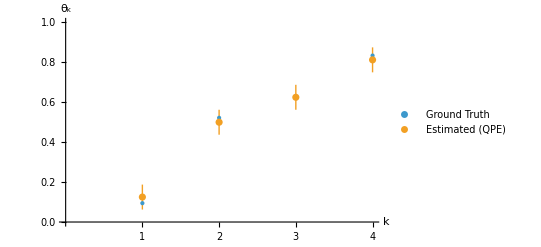

```mathematica
ListPlot[{Sort@θ2,Around[combinedestimates,2^-4]},]
```

While the applications are beyond the scope of this lesson, efficient computation of matrix eigenvalues allows many shortcuts in understanding the stability and solution space of a wide range of quantitative models. For more on the uses of eigenvalues and eigenvectors, see the Introduction to Linear Algebra.